## RNN Sequence 10

```mathematica
normalizedLoadTS=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\normalizedLoadTS.wxf"]
```

TimeSeries[…]

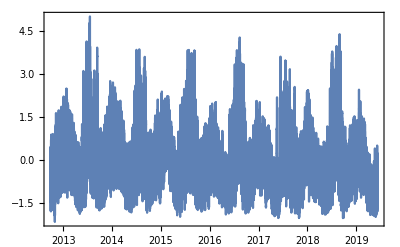

```mathematica
DateListPlot[normalizedLoadTS]
```

```mathematica
data=normalizedLoadTS//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,20,1];valuesp = values[[21;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,20}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

58660

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",20}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

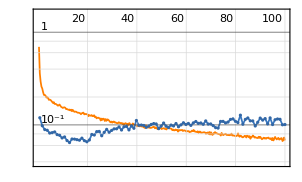
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:8.2min  examples/s:9245
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.99×10^-2
validation | ,,  loss:1.01×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.0516071|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{0.480808,0.511368,0.472699,0.37762,0.293784,0.263704,0.276773,0.405239,0.592417,0.685228,0.743314,0.541233,0.155575,-0.327522,-0.650725,-0.818252,-0.933706,-0.994226,-0.985986,-0.973951}}→-0.685315,{{-1.21784,-1.3583,-1.38597,-1.36645,-1.23204,-1.07085,-0.669235,-0.354606,-0.332578,-0.375,-0.33066,-0.355133,-0.434928,-0.322766,-0.380464,-0.23067,-0.0381398,-0.0323069,-0.00979827,0.101038}}→0.0576084}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:8.2min  examples/s:9245
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.99×10^-2
validation | ,,  loss:1.01×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{-1.21784,-1.3583,-1.38597,-1.36645,-1.23204,-1.07085,-0.669235,-0.354606,-0.332578,-0.375,-0.33066,-0.355133,-0.434928,-0.322766,-0.380464,-0.23067,-0.0381398,-0.0323069,-0.00979827,0.101038}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100];
```

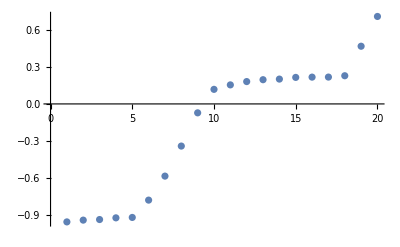

```mathematica
ListPlot[results]
```